# Phasenraum für Pendel mittels 4th-Order Runge Kutta

```mathematica
<<VectorAnalysis`
```

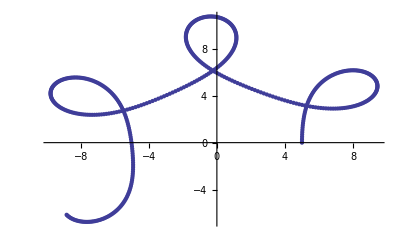

```mathematica
f[u_]:={-u[[2]]/Norm[u[[2]]]^3-e-CrossProduct[u[[1]],b],u[[1]]}
h=0.2;n=1000;Z=0;u={{0,0.5,0},{5,0,0}};U={u};
e={0,0,0};b={0,0,-0.1};
Do[
	Z++;

		k0=h*f[u];k1=h*f[u+k0/2];k2=h*f[u+k1/2];k3=h*f[u+k2];
		u+=1/6*(k0+2 k1+2 k2+k3);
If[Mod[Z,2]==1,
	AppendTo[U,u];];

	


,{n}]
ListPlot[#[[2]][[1;;2]]&/@U]
```

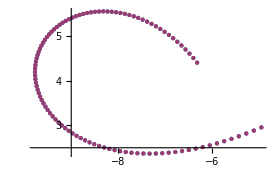

```mathematica
a=300;b=400;ListPlot[{#[[2]][[1;;2]]&/@U[[a;;b]],#[[2]][[1;;2]]&/@F[[a;;b]]}]
```

```mathematica
U[[400;;400]]
```

{{{0.199919,-0.264362,0.},{-6.31175,4.40444,0.}}}

```mathematica
F=U;
```

```mathematica
#[[2]][[1;;2]]&/@U [[5;;8]]
```

{{-0.08,-0.08},{-0.125,-0.125},{-0.18,-0.18},{-0.245,-0.245}}

{{-0.0399893,-0.000799893,0.},{-0.000799893,-0.0000106658,0.}}

```mathematica
Exit[]
```

```mathematica
a=3
```

3